```mathematica
ClearAll["`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
Aqmeas={#[[1]],Around[#[[2]],#[[3]]]}&/@Import["Aq_measure.csv"];
Aqfit=Import["Aq_fit.csv"];
AqJoin=Join[Aqmeas,Aqfit,2];
Agmeas={#[[1]],Around[#[[2]],#[[3]]]}&/@Import["Ag_measure.csv"];
Agfit=Import["Ag_fit.csv"];
AgJoin=Join[Agmeas,Agfit,2];
Dqmeas={#[[1]],Around[#[[2]],#[[3]]]}&/@Import["Dq_measure.csv"];
Dqfit=Import["Dq_fit.csv"];
DqJoin=Join[Dqmeas,Dqfit,2];
Dgmeas={#[[1]],Around[#[[2]],#[[3]]]}&/@Import["Dg_measure.csv"];
Dgfit=Import["Dg_fit.csv"];
DgJoin=Join[Dgmeas,Dgfit,2];
dsigmameas={#[[1]],#[[2]],Around[#[[3]],#[[4]]]}&/@Import["dsigma_select_measure.csv"];
dsigmafit=Import["dsigma_select_fit.csv"];
dsigmaJoin=Join[dsigmameas,dsigmafit,2];
```

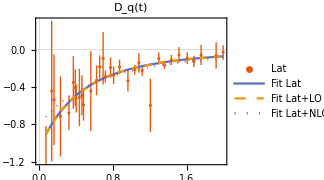

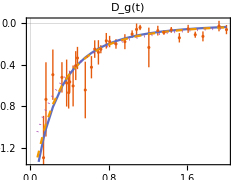

```mathematica
Aqplt=ListPlot[{AqJoin[[All,{1,2}]],AqJoin[[All,{1,3}]],AqJoin[[All,{1,4}]],AqJoin[[All,{1,5}]]},PlotTheme->"Scientific",Joined->{False,True,True,True},PlotStyle->{Automatic,Line,Dashed,Dotted},AspectRatio->3/4,ImageSize->240,PlotLabel->"A_q(t)"];
Agplt=ListPlot[{AgJoin[[All,{1,2}]],AgJoin[[All,{1,3}]],AgJoin[[All,{1,4}]],AgJoin[[All,{1,5}]]},PlotTheme->"Scientific",Joined->{False,True,True,True},PlotStyle->{Automatic,Line,Dashed,Dotted},AspectRatio->3/4,ImageSize->240,PlotLabel->"A_g(t)"];
Dqplt=ListPlot[{DqJoin[[All,{1,2}]],DqJoin[[All,{1,3}]],DqJoin[[All,{1,4}]],DqJoin[[All,{1,5}]]},PlotTheme->"Scientific",Joined->{False,True,True,True},PlotStyle->{Automatic,Line,Dashed,Dotted},PlotLegends->Placed[{"Lat","Fit Lat","Fit Lat+LO Exp","Fit Lat+NLO Exp"},Right],AspectRatio->3/4,ImageSize->240,PlotLabel->"D_q(t)"]
Dgplt=ListPlot[{DgJoin[[All,{1,2}]],DgJoin[[All,{1,3}]],DgJoin[[All,{1,4}]],DgJoin[[All,{1,5}]]},PlotTheme->"Scientific",Joined->{False,True,True,True},PlotStyle->{Automatic,Line,Dashed,Dotted},AspectRatio->3/4,ImageSize->240,PlotLabel->"D_g(t)"]
```

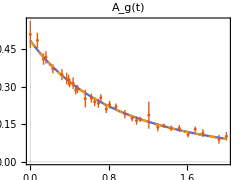
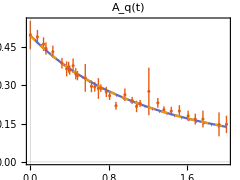
-Graphics- | -Graphics-
-Graphics- | -Graphics-

FFplt.png

```mathematica
Grid[{{Agplt,Aqplt},{Dgplt,Dqplt}},Alignment->Left]
Export["FFplt.png",%,ImageResolution->300]
```

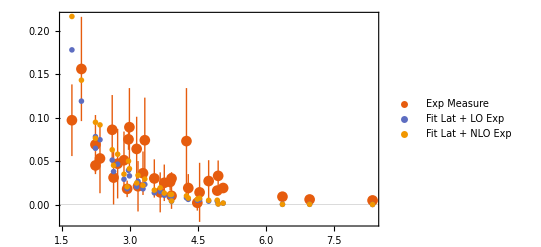

xsec.png

```mathematica
ListPlot[{dsigmaJoin[[All,{2,3}]],dsigmaJoin[[All,{2,4}]],dsigmaJoin[[All,{2,5}]]},PlotMarkers->{Automatic,"OpenMarkers","OpenMarkers"},PlotLegends->{"Exp Measure","Fit Lat + LO Exp","Fit Lat + NLO Exp"},PlotTheme->"Scientific",ImageSize->400]
Export["xsec.png",%,ImageResolution->300]
```